```mathematica
Quit[]
```

total number of errors and warnings
===================================
fferr: no errors

```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
$FAVerbose=0;
```

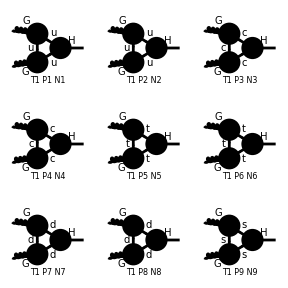

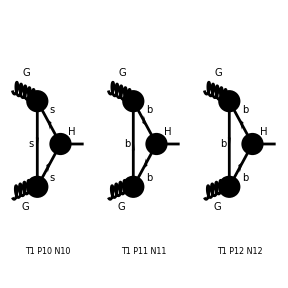

FeynArtsGraphics({G,G}→{H})(([T1 P1 N1] | [T1 P2 N2] | [T1 P3 N3]
[T1 P4 N4] | [T1 P5 N5] | [T1 P6 N6]
[T1 P7 N7] | [T1 P8 N8] | [T1 P9 N9]),([T1 P10 N10] | [T1 P11 N11] | [T1 P12 N12]
Null | Null | Null
Null | Null | Null))

```mathematica
diags=InsertFields[CreateTopologies[1,2->1,ExcludeTopologies->{SelfEnergies}],{V[4],V[4]}->{S[1]},InsertionLevel->{Particles},Model->"htt",GenericModel->"htt",ExcludeParticles->{F[4,{1,o}],F[4,{2,o}],F[4,{3,o}],F[3,{1,o}],F[3,{2,o}]}];
Paint[diags]
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[diags,Truncated->True],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3]},LoopMomenta->{l},DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True]/.M$FACouplings/.{FCGV["MT"]->MT,FAGS->gs,ybcky->yt};
```

```mathematica
ampt=amp[[5]]+amp[[6]]//Contract//TR//SUNSimplify//FullSimplify//ChangeDimension[#,D]&;
```

```mathematica
ampt
```

(ⅈ gs^2 MT yt δ^Glu1Glu2 (cos(al) (g^Lor1Lor2 (-l^2+MT^2+(p(2))^2-p(2)·p(3))+2 l^Lor1 (2 l^Lor2+(p(2))^Lor2)-(p(3))^Lor1 (2 l^Lor2+(p(2))^Lor2)+(p(2))^Lor1 (2 l^Lor2+(p(3))^Lor2))+sin(al) ϵ^(Lor1Lor2p(2)p(3))))/(√2 π^4 (l^2-MT^2).((l+p(2))^2-MT^2).((l+p(2)-p(3))^2-MT^2))

```mathematica
ampt=ampt/.{p[3]->p[1]+p[2]}
```

(ⅈ gs^2 MT yt δ^Glu1Glu2 (cos(al) (g^Lor1Lor2 (-p(2)·(p(1)+p(2))-l^2+MT^2+(p(2))^2)+2 l^Lor1 (2 l^Lor2+(p(2))^Lor2)-(p(1)+p(2))^Lor1 (2 l^Lor2+(p(2))^Lor2)+(p(2))^Lor1 (2 l^Lor2+(p(1)+p(2))^Lor2))+sin(al) ϵ^(Lor1Lor2p(2)p(1)+p(2))))/(√2 π^4 (l^2-MT^2).((l+p(2))^2-MT^2).((l+p(2)-(p(1)+p(2)))^2-MT^2))

```mathematica
FCClearScalarProducts[];
SPD[p[1],p[1]]=0;
SPD[p[2],p[2]]=q;
SPD[p[1],p[2]]=(MH^2-q)/2;
```

```mathematica
ampt=TID[ampt,l,ToPaVe->True]//Simplify;
```

```mathematica
ampt
```

-1/(2 √2 π^2 (D-2) (MH^2-q)^3)gs^2 MT yt δ^Glu1Glu2 (-(MH^2-q) (4 (D-2) cos(al) (p(1))^Lor1 B_0(0,MT^2,MT^2) ((p(2))^Lor2 (q-MH^2)+2 q (p(1))^Lor2)+C_0(0,q,MH^2,MT^2,MT^2,MT^2) (cos(al) (MH^2-q)^2 g^Lor1Lor2 ((D-2) MH^2-(D-2) q-8 MT^2)-2 (MH^2-q) (cos(al) (p(2))^Lor1 (p(1))^Lor2 ((D-2) MH^2-(D-2) q-8 MT^2)-(D-2) sin(al) (MH^2-q) ϵ^(Lor1Lor2p(1)p(2)))+2 cos(al) (p(1))^Lor1 ((D-2) MH^2+(D-2) q+8 MT^2) ((p(2))^Lor2 (MH^2-q)-2 q (p(1))^Lor2)))-4 cos(al) B_0(q,MT^2,MT^2) (-(p(1))^Lor1 ((D-2) MH^2+D q) ((p(2))^Lor2 (MH^2-q)-2 q (p(1))^Lor2)+q (MH^2-q)^2 g^Lor1Lor2+2 q (p(2))^Lor1 (p(1))^Lor2 (q-MH^2))-2 cos(al) B_0(MH^2,MT^2,MT^2) ((MH^2-q)^2 ((D-4) MH^2-(D-2) q) g^Lor1Lor2-2 (p(2))^Lor1 (p(1))^Lor2 (MH^2-q) ((D-4) MH^2-(D-2) q)+2 (p(1))^Lor1 (D (MH^2+q)-2 q) ((p(2))^Lor2 (MH^2-q)-2 q (p(1))^Lor2)))

```mathematica
Cases[ampt,_B0,Infinity]//DeleteDuplicates//StandardForm
```

{B0[q,MT^2,MT^2],B0[MH^2,MT^2,MT^2],B0[0,MT^2,MT^2]}

```mathematica
Cases[ampt,_C0,Infinity]//DeleteDuplicates//StandardForm
```

{C0[Pair[Momentum[p[1],D],Momentum[p[1],D]],Pair[Momentum[p[2],D],Momentum[p[2],D]],Pair[Momentum[p[1],D],Momentum[p[1],D]]+2 Pair[Momentum[p[1],D],Momentum[p[2],D]]+Pair[Momentum[p[2],D],Momentum[p[2],D]],MT^2,MT^2,MT^2]}

```mathematica
beta=Sqrt[4 MT^2/MH^2-1];
beta1=Sqrt[1-4 MT^2/q];
scalarIntegral={_C0->(1/2/(q-MH^2) (Log[(beta1+1)/(beta1-1)]^2+ ArcTan[2 beta/(1-beta^2)]^2)),
B0[MH^2,MT^2,MT^2]->(1/ep+Log[m^2/MH^2]+2-beta ArcTan[2 beta/(beta^2-1)]-Log[(1+beta^2)/4]),
B0[q,MT^2,MT^2]->(1/ep+Log[m^2/(-q)]+2+beta1 Log[beta1-1]-beta1 Log[beta1+1]-Log[(beta1^2-1)/4]),
B0[0,MT^2,MT^2]->(1/ep+Log[m^2/MT^2])};
```

```mathematica
tmp=Series[ampt/.scalarIntegral//ChangeDimension[#,4]&//ReplaceAll[#,{D->4-2 ep}]&,{ep,0,0}]//Normal//Simplify
```

1/(4 √2 π^2 (MH^2-q)^3)gs^2 MT yt δ^Glu1Glu2 (4 cos(al) (log(-m^2/q)+√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)-1)-√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)+1)-log(-MT^2/q)+2) (q (MH^2-q)^2 (ḡ)^Lor1Lor2+2 q (q-MH^2) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2-2 (MH^2+2 q) OverBar[p(1)]^Lor1 ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))+2 cos(al) (log(m^2/MH^2)-log(MT^2/MH^2)+√((4 MT^2)/MH^2-1) tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2))+2) (-2 q (MH^2-q)^2 (ḡ)^Lor1Lor2+4 q (MH^2-q) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2+4 (2 MH^2+q) OverBar[p(1)]^Lor1 ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))-1/2 ((tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2+log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))) (2 cos(al) (MH^2-q)^2 (MH^2-4 MT^2-q) (ḡ)^Lor1Lor2-2 (MH^2-q) (2 cos(al) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2 (MH^2-4 MT^2-q)+2 sin(al) (q-MH^2) ϵ^(Lor1Lor2 OverBar[p(1)]OverBar[p(2)]))+4 cos(al) OverBar[p(1)]^Lor1 (MH^2+4 MT^2+q) ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))-4 cos(al) (MH^2-q)^3 (ḡ)^Lor1Lor2-4 cos(al) (MH^2-q) OverBar[p(1)]^Lor1 (2-2 log(m^2/MT^2)) ((q-MH^2) OverBar[p(2)]^Lor2+2 q OverBar[p(1)]^Lor2)+8 cos(al) (MH^2-q)^2 OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2)

```mathematica
Cases[tmp,_Pair,Infinity]//DeleteDuplicates//StandardForm
```

{Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]],Pair[LorentzIndex[Lor1],Momentum[p[2]]],Pair[LorentzIndex[Lor2],Momentum[p[1]]],Pair[LorentzIndex[Lor1],Momentum[p[1]]],Pair[LorentzIndex[Lor2],Momentum[p[2]]]}

```mathematica
Cases[tmp,_Eps,Infinity]//DeleteDuplicates//StandardForm
```

{Eps[LorentzIndex[Lor1],LorentzIndex[Lor2],Momentum[p[1]],Momentum[p[2]]]}

```mathematica
?CoefficientList
```

```mathematica
Coefficient[tmp,Pair[LorentzIndex[Lor1],Momentum[p[1]]] Pair[LorentzIndex[Lor2],Momentum[p[1]]]]//Simplify
```

1/(√2 π^2 (MH^2-q)^3)gs^2 MT q yt cos(al) δ^Glu1Glu2 (4 (MH^2-q) (log(m^2/MT^2)-1)+4 (MH^2+2 q) (log(-m^2/q)+√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)-1)-√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)+1)-log(-MT^2/q)+2)-4 (2 MH^2+q) (log(m^2/MH^2)-log(MT^2/MH^2)+√((4 MT^2)/MH^2-1) tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2))+2)+(MH^2+4 MT^2+q) ((tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2+log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))))

```mathematica
tmp
```

1/(4 √2 π^2 (MH^2-q)^3)gs^2 MT yt δ^Glu1Glu2 (4 cos(al) (log(-m^2/q)+√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)-1)-√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)+1)-log(-MT^2/q)+2) (q (MH^2-q)^2 (ḡ)^Lor1Lor2+2 q (q-MH^2) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2-2 (MH^2+2 q) OverBar[p(1)]^Lor1 ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))+2 cos(al) (log(m^2/MH^2)-log(MT^2/MH^2)+√((4 MT^2)/MH^2-1) tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2))+2) (-2 q (MH^2-q)^2 (ḡ)^Lor1Lor2+4 q (MH^2-q) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2+4 (2 MH^2+q) OverBar[p(1)]^Lor1 ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))-1/2 ((tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2+log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))) (2 cos(al) (MH^2-q)^2 (MH^2-4 MT^2-q) (ḡ)^Lor1Lor2-2 (MH^2-q) (2 cos(al) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2 (MH^2-4 MT^2-q)+2 sin(al) (q-MH^2) ϵ^(Lor1Lor2 OverBar[p(1)]OverBar[p(2)]))+4 cos(al) OverBar[p(1)]^Lor1 (MH^2+4 MT^2+q) ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))-4 cos(al) (MH^2-q)^3 (ḡ)^Lor1Lor2-4 cos(al) (MH^2-q) OverBar[p(1)]^Lor1 (2-2 log(m^2/MT^2)) ((q-MH^2) OverBar[p(2)]^Lor2+2 q OverBar[p(1)]^Lor2)+8 cos(al) (MH^2-q)^2 OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2)

```mathematica
structure=Coefficient[tmp,{Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]],Pair[LorentzIndex[Lor1],Momentum[p[2]]] Pair[LorentzIndex[Lor2],Momentum[p[1]]],Pair[LorentzIndex[Lor2],Momentum[p[2]]] Pair[LorentzIndex[Lor1],Momentum[p[1]]],Pair[LorentzIndex[Lor2],Momentum[p[1]]] Pair[LorentzIndex[Lor1],Momentum[p[1]]],Eps[LorentzIndex[Lor1],LorentzIndex[Lor2],Momentum[p[1]],Momentum[p[2]]]}]//Simplify;
```

```mathematica
structure[[1]]=structure[[1]]/SPD[p[1],p[2]];
```

```mathematica
structure/.{MH->125,m->1,MT->172,q->-1000000}//N//Simplify
```

{-0.0000509941 gs^2 yt cos(al) δ^Glu1Glu2,0.0000509941 gs^2 yt cos(al) δ^Glu1Glu2,6.63632×10^-6 gs^2 yt cos(al) δ^Glu1Glu2,0.0000130684 gs^2 yt cos(al) δ^Glu1Glu2,-0.0000809884 gs^2 yt sin(al) δ^Glu1Glu2}

```mathematica
structure[[4]]
```

1/(√2 π^2 (MH^2-q)^3)gs^2 MT q yt cos(al) δ^Glu1Glu2 (4 (MH^2-q) (log(m^2/MT^2)-1)+4 (MH^2+2 q) (log(-m^2/q)+√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)-1)-√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)+1)-log(-MT^2/q)+2)-4 (2 MH^2+q) (log(m^2/MH^2)-log(MT^2/MH^2)+√((4 MT^2)/MH^2-1) tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2))+2)+(MH^2+4 MT^2+q) ((tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2+log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))))